# Homework 12

## Problem 12.1

A 5.00 g mass made of iron hangs vertically from a spring of spring constant 6.00 N/m.  It is driven sinusoidally by an electromagnet that provides a maximum force 0.0005 N on the mass.The system is characterized by a damping constant of beta = 2 s^-1.

## Part A

(A) Write down the differential equation for the system with the driving frequency omega left as a variable. Plot the early and late behavior of the system for three driving frequencies : 2 omega0, 1/2 omega0 and omega0. Take the initial conditions to be x (0) = 0 m and v (0) = 0.

Write the differential equation for the driven oscillator. Let the driving force be given by f0*cos(omega*t).

### ω=2 ω_0

```mathematica
Quit[]
```

-2.30531×10^-21 Cos[0.115566 t]-0.0000276141 Cos[69.282 t]+(0.+1.80103×10^-23 ⅈ) Cos[138.448 t]+1.44082×10^-22 Sin[0.115566 t]+ⅇ^(-2. t) (0.0000276141 Cos[34.5832 t]-2.66161×10^-6 Sin[34.5832 t])+2.12574×10^-6 Sin[69.282 t]-3.60205×10^-23 Sin[138.448 t]

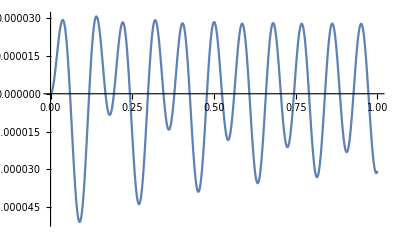

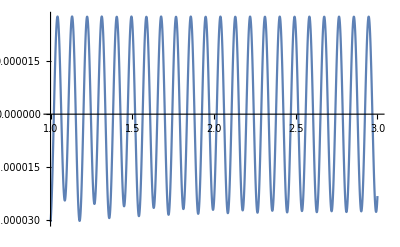

```mathematica
beta=2;
m=.005;
k=6;
f0=.0005/m;
omega0=Sqrt[k/m];
omega=2*omega0;
eq1=x''[t]+2*beta*x'[t]+x[t]*omega0^2== f0*Cos[omega*t];
DSolve[{eq1,x[0]==0,x'[0]==0},x[t],t];
sol=FullSimplify[%];
x[t_]=x[t]/.sol[[1]]
Plot[x[t],{t,0,1}]
Plot[x[t],{t,1,3}]
```

### ω=ω_0/2

Copy and paste the cell above but change the value of omega to omega0 / 2. Be sure to sure the Quit[] function to avoid problems executing the code.

```mathematica
Quit[]
```

1.82642×10^-20 Cos[0.231715 t]-0.000108538 Cos[34.641 t]-4.56606×10^-21 Cos[69.0503 t]+ⅇ^(-2. t) (0.000108538 Cos[17.2047 t]-0.0000210289 Sin[17.2047 t])+0.0000167106 Sin[34.641 t]

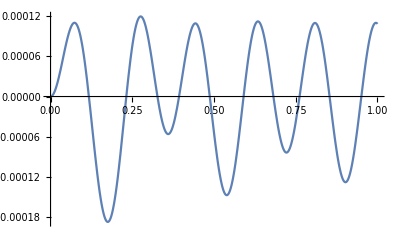

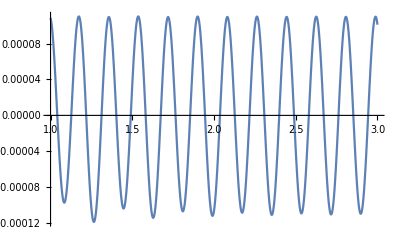

```mathematica
beta=2;
m=.005;
k=6;
f0=.0005/m;
omega0=Sqrt[k/m]/2;
omega=2*omega0;
eq1=x''[t]+2*beta*x'[t]+x[t]*omega0^2== f0*Cos[omega*t];
DSolve[{eq1,x[0]==0,x'[0]==0},x[t],t];
sol=FullSimplify[%];
x[t_]=x[t]/.sol[[1]]
Plot[x[t],{t,0,1}]
Plot[x[t],{t,1,3}]
```

### ω=ω_0

Now do the same for omega = omega0. Be sure to sure the Quit[] function to avoid problems executing the code.

```mathematica
Quit[]
```

1.19601×10^-18 Cos[34.641 t]+(2.31683×10^-21-3.62005×10^-23 ⅈ) Cos[103.807 t]+ⅇ^(-2. t) (-1.73472×10^-18 Cos[34.5832 t]-(0.000722894-4.53262×10^-24 ⅈ) Sin[34.5832 t])+0.000721688 Sin[34.641 t]-3.62005×10^-23 Sin[103.807 t]

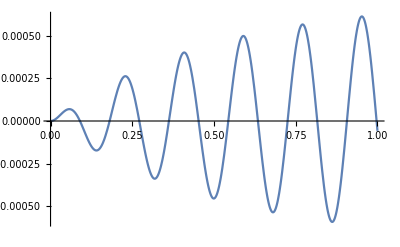

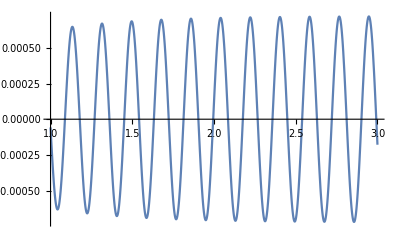

```mathematica
beta=2;
m=.005;
k=6;
f0=.0005/m;
omega0=Sqrt[k/m];
omega=omega0;
eq1=x''[t]+2*beta*x'[t]+x[t]*omega0^2== f0*Cos[omega*t];
DSolve[{eq1,x[0]==0,x'[0]==0},x[t],t];
sol=FullSimplify[%];
x[t_]=x[t]/.sol[[1]]
Plot[x[t],{t,0,1}]
Plot[x[t],{t,1,3}]
```

Based on your graphs, estimate the maximum amplitude for steady state oscillation for the ω=ω_0 case.

```mathematica
A0est=.0007;
```

### Solution

```mathematica
A=.7216878365*10^-3;
If[Abs[A0est-A]/A<.06,Print["Estimate for A is correct"],Print["Estimate for A is not correct"]]
If[Abs[A0est*10-A]/A<.06,Print["Did you remember to nclude f0 in your driving forces?"]]
```

Estimate for A is correct

## Part B

From the solution of the last differential equation above, find the part that corresponds to the steady state solution and cut and paste it into the function below. Remove very small terms - particularly the imaginary parts that should be zero. Plot this function and find the maximum amplitude of the solution from the equation.

```mathematica
Quit[]
```

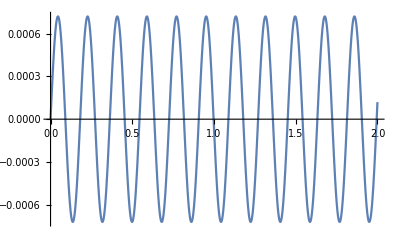

```mathematica
xss=0.0007216878364870322 Sin[34.64101615137755 t];
Plot[xss,{t,0,2}]
```

```mathematica
A0=0.0007216878364870322;
```

### Solution

```mathematica
A=.7216878365*10^-3;
If[Abs[A0-A]/A<.001,Print["A0 is correct"],Print["A0 is not correct"]]
```

A0 is correct

## Written Problems

-Graphics-